```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
range100=DeleteCases[Range[-100,100],0];
range200=DeleteCases[Range[-200,200],0];
```

```mathematica
LaunchKernels[8];(* To launch kernels for Parallel tasks *)
```

```mathematica
(*net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];*)
```

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
theta1byΔu0[k_, nq_, qInPower_] := allprodθbyΔ[1,k, 2, 0, 3, 0, 4, 0, nq, 0,qInPower]
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
theta3byΔu0[m_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, m, 4, 0, nq, 0,qInPower]
theta4byΔu0[n_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, 0, 4, n, nq, 0,qInPower]
```

```mathematica
allprodθwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_, qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq,cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
(*cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,q^((k+l)/4+mnnonzero-qInPower)Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
(*dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];*)
dt =Join[cq2[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq2]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
klmnpos[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnposonly[rng_,n_]:= Values[FindInstance[{0<a<rng, 0<b<rng, 0<c<rng,0<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnneg[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d<0},{a,b,c,d},Integers, n]];
klmnnegonly[rng_,n_]:= Values[FindInstance[{-rng<a<0, -rng<b<0, -rng<c<0, -rng<d<0, a+b+c+d<0},{a,b,c,d},Integers, n]];
```

```mathematica
powerspos[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
powersneg[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]<0]
```

```mathematica
allprodgen[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn.txt";
filename2=NotebookDirectory[]<>"monitor.txt";   (*For positive powers*)
(*filename=NotebookDirectory[]<>"jacobi-klmn-neg-only.txt";
filename2=NotebookDirectory[]<>"monitor-neg-only.txt";*)
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenneg[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitor-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenbyΔneg[nq_,nu_,pwrlistref_,pwrlist_,qInPower_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobibyΔ-klmn-neg1.txt";
filename2=NotebookDirectory[]<>"monitorbyΔ-neg1.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθbyΔwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu,qInPower}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
listtorule[list_] := list[[;;-2]] -> list[[-1]]
```

```mathematica
extractMF[data_]:=Module[{data2,data3,data4,data5,mfdata,indices,indlens,i},
data2=StringDelete[StringDelete[data," "],"\n"];
indices=Union/@StringPosition[data2,"{"]//Flatten;
indlens=indices[[#+1]]-indices[[#]]&/@Range[Length[indices]-1];
data3=Table[StringTake[data2,{indices[[i+1]],indices[[i+2]]-2}],{i,Length[indlens]-1}];
data4=ToExpression/@data3/.{$Failed->Nothing,Null->Nothing}//Quiet;
data5=Cases[data4,x_/;Length[x]>4];
mfdata=listtorule/@data5;
Return[mfdata]
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## θ_1^k θ_2^l θ_3^m θ_4^n/Δ

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
plist=klmnneg[5, 400];
```

```mathematica
allprodgenbyΔneg[50,70,plist,plist[[66;;70]],0];
```

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
Length[data1]
```

563

```mathematica
data1[[1]]
```

{1/2,3,12,40,120,330,848,2064,9615/2,10780,23388,49296,101288,203400,400080,772256,2930433/2,2736282,5035680,9142200,16388712,29033368,50866080,88191120,151407455,257531352,434197212,725960752,1204168800,1982320320,3239841904,5258684832,16958732355/2,13586349820,21637508640,34259509536,53941372880,84473619042,131602478160,204000540720,314701294542,483211205016,738607986368,1124069367840,1703470012200,2570958824792,3864817983600,5787454432416,17268297384805/2,12834273269640,19010217094956}→-9/2

#### jacobi-klmn-neg, Net0, 40 coeffs

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{37}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

NetChain::invindata3: Data supplied to port "Input" could not be encoded; "Function" encoder did not produce an output that was a length-43 vector of real numbers.

General::stop: Further output of NetChain::invindata3 will be suppressed during this calculation.

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

#### jacobi-klmn-neg, Net3, 40 coeffs

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
datasize = Length[data]
```

7221

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
(*Length /@ Keys[traindata] // Union
Length /@ Keys[valdata] // Union
Length /@ Keys[testdata] // Union*)
```

```mathematica
Length @ Keys[traindata[[914]]]
```

40

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrain::encgenfail1: Could not encode training input number 914 for port "Input": "Function" encoder did not produce an output that was a length-40 vector of real numbers. Please check the example.

$Failed

Set::shape: Lists {tNet,valLosses} and $Failed[{TrainedNet,ValidationLossList}] are not the same shape.

$Failed[{TrainedNet,ValidationLossList}]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

NetChain::invindata3: Data supplied to port "Input" could not be encoded; "Function" encoder did not produce an output that was a length-43 vector of real numbers.

General::stop: Further output of NetChain::invindata3 will be suppressed during this calculation.

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1/719 (40/3 Abs[-15/2-$Failed]+800/11 Abs[-11/2-$Failed]+1000/9 Abs[-9/2-$Failed]+1800/7 Abs[-7/2-$Failed]+280 Abs[-5/2-$Failed]+1400/3 Abs[-3/2-$Failed]+1800 Abs[-1/2-$Failed]+1600 Abs[1/2-$Failed]+700 Abs[1-$Failed]+2200/3 Abs[3/2-$Failed]+450 Abs[2-$Failed]+360 Abs[5/2-$Failed]+800/3 Abs[3-$Failed]+1600/7 Abs[7/2-$Failed]+250 Abs[4-$Failed]+2000/9 Abs[9/2-$Failed]+80 Abs[5-$Failed]+1400/11 Abs[11/2-$Failed]+550/3 Abs[6-$Failed]+1000/13 Abs[13/2-$Failed]+800/7 Abs[7-$Failed]+440/3 Abs[15/2-$Failed]+75 Abs[8-$Failed]+2600/17 Abs[17/2-$Failed]+400/9 Abs[9-$Failed]+2400/19 Abs[19/2-$Failed]+40 Abs[10-$Failed]+1200/7 Abs[21/2-$Failed]+700/11 Abs[11-$Failed]+2200/23 Abs[23/2-$Failed]+50 Abs[12-$Failed]+104 Abs[25/2-$Failed]+1000/13 Abs[13-$Failed]+800/9 Abs[27/2-$Failed]+250/7 Abs[14-$Failed]+1400/29 Abs[29/2-$Failed]+200/3 Abs[15-$Failed]+1000/31 Abs[31/2-$Failed]+75/2 Abs[16-$Failed]+2600/33 Abs[33/2-$Failed]+900/17 Abs[17-$Failed]+360/7 Abs[35/2-$Failed]+350/9 Abs[18-$Failed]+2000/37 Abs[37/2-$Failed]+1200/19 Abs[19-$Failed]+2000/39 Abs[39/2-$Failed]+60 Abs[20-$Failed]+2600/41 Abs[41/2-$Failed]+100/7 Abs[21-$Failed]+1600/43 Abs[43/2-$Failed]+400/11 Abs[22-$Failed]+80/3 Abs[45/2-$Failed]+1000/23 Abs[23-$Failed]+1800/47 Abs[47/2-$Failed]+25 Abs[24-$Failed]+1800/49 Abs[49/2-$Failed]+36 Abs[25-$Failed]+600/17 Abs[51/2-$Failed]+350/13 Abs[26-$Failed]+600/53 Abs[53/2-$Failed]+700/27 Abs[27-$Failed]+320/11 Abs[55/2-$Failed]+275/7 Abs[28-$Failed]+2800/57 Abs[57/2-$Failed]+800/29 Abs[29-$Failed]+1200/59 Abs[59/2-$Failed]+30 Abs[30-$Failed]+1000/61 Abs[61/2-$Failed]+1000/31 Abs[31-$Failed]+2000/63 Abs[63/2-$Failed]+275/8 Abs[32-$Failed]+160/13 Abs[65/2-$Failed]+500/33 Abs[33-$Failed]+1200/67 Abs[67/2-$Failed]+200/17 Abs[34-$Failed]+800/69 Abs[69/2-$Failed]+20/7 Abs[35-$Failed]+1400/71 Abs[71/2-$Failed]+125/9 Abs[36-$Failed]+800/73 Abs[73/2-$Failed]+300/37 Abs[37-$Failed]+32/3 Abs[75/2-$Failed]+150/19 Abs[38-$Failed]+2000/77 Abs[77/2-$Failed]+600/79 Abs[79/2-$Failed]+5/2 Abs[40-$Failed]+400/81 Abs[81/2-$Failed]+100/41 Abs[41-$Failed]+800/83 Abs[83/2-$Failed]+100/21 Abs[42-$Failed]+160/17 Abs[85/2-$Failed]+25/11 Abs[44-$Failed]+200/89 Abs[89/2-$Failed]+400/93 Abs[93/2-$Failed]+40/19 Abs[95/2-$Failed]+800 Abs[1+$Failed]+200 Abs[2+$Failed]+800/3 Abs[3+$Failed]+125 Abs[4+$Failed]+200 Abs[5+$Failed]+50 Abs[6+$Failed]+25/2 Abs[8+$Failed])

## Rough

```mathematica
t2 = Series[EllipticTheta[2,u,q],{q,0,7}, {u,0,10}]
Collect[t2,u]
```

(2-u^2+u^4/12-u^6/360+u^8/20160-u^10/1814400+O[u]^11) q^(1/4)+(2-9 u^2+(27 u^4)/4-(81 u^6)/40+(729 u^8)/2240-(729 u^10)/22400+O[u]^11) q^(9/4)+(2-25 u^2+(625 u^4)/12-(3125 u^6)/72+(78125 u^8)/4032-(390625 u^10)/72576+O[u]^11) q^(25/4)+O[q]^(29/4)

2 q^(1/4)+2 q^(9/4)+2 q^(25/4)+(-q^(1/4)-9 q^(9/4)-25 q^(25/4)) u^2+(q^(1/4)/12+(27 q^(9/4))/4+(625 q^(25/4))/12) u^4+(-q^(1/4)/360-(81 q^(9/4))/40-(3125 q^(25/4))/72) u^6+(q^(1/4)/20160+(729 q^(9/4))/2240+(78125 q^(25/4))/4032) u^8+(-q^(1/4)/1814400-(729 q^(9/4))/22400-(390625 q^(25/4))/72576) u^10

```mathematica
t2 = Series[EllipticTheta[3,u,q]^-2,{q,0,7},{u,0,10}]
Collect[t2,u]
```

1+(-4+8 u^2-(8 u^4)/3+(16 u^6)/45-(8 u^8)/315+(16 u^10)/14175+O[u]^11) q+(12-48 u^2+64 u^4-(512 u^6)/15+(1024 u^8)/105-(8192 u^10)/4725+O[u]^11) q^2+(-32+192 u^2-448 u^4+(7808 u^6)/15-(35008 u^8)/105+(89984 u^10)/675+O[u]^11) q^3+(76-608 u^2+(6272 u^4)/3-(173056 u^6)/45+(1329152 u^8)/315-(6012928 u^10)/2025+O[u]^11) q^4+(-168+1680 u^2-7664 u^4+(59360 u^6)/3-(476432 u^8)/15+(32005856 u^10)/945+O[u]^11) q^5+(352-4224 u^2+24064 u^4-(1212416 u^6)/15+(18325504 u^8)/105-(1212809216 u^10)/4725+O[u]^11) q^6+(-704+9856 u^2-(202624 u^4)/3+(12660992 u^6)/45-(34794112 u^8)/45+(20941935872 u^10)/14175+O[u]^11) q^7+O[q]^8

1-4 q+12 q^2-32 q^3+76 q^4-168 q^5+352 q^6-704 q^7+(8 q-48 q^2+192 q^3-608 q^4+1680 q^5-4224 q^6+9856 q^7) u^2+(-(8 q)/3+64 q^2-448 q^3+(6272 q^4)/3-7664 q^5+24064 q^6-(202624 q^7)/3) u^4+((16 q)/45-(512 q^2)/15+(7808 q^3)/15-(173056 q^4)/45+(59360 q^5)/3-(1212416 q^6)/15+(12660992 q^7)/45) u^6+(-(8 q)/315+(1024 q^2)/105-(35008 q^3)/105+(1329152 q^4)/315-(476432 q^5)/15+(18325504 q^6)/105-(34794112 q^7)/45) u^8+((16 q)/14175-(8192 q^2)/4725+(89984 q^3)/675-(6012928 q^4)/2025+(32005856 q^5)/945-(1212809216 q^6)/4725+(20941935872 q^7)/14175) u^10

2 q^(1/4)+2 q^(9/4)+2 q^(25/4)+(-q^(1/4)-9 q^(9/4)-25 q^(25/4)) u^2+(q^(1/4)/12+(27 q^(9/4))/4+(625 q^(25/4))/12) u^4+(-q^(1/4)/360-(81 q^(9/4))/40-(3125 q^(25/4))/72) u^6+(q^(1/4)/20160+(729 q^(9/4))/2240+(78125 q^(25/4))/4032) u^8+(-q^(1/4)/1814400-(729 q^(9/4))/22400-(390625 q^(25/4))/72576) u^10

```mathematica
t2nou = Series[EllipticTheta[2,0,q]^-3,{q,0,7} ]
Collect[t2nou, u]
```

1/(8 q^(3/4))-(3 q^(5/4))/8+(3 q^(13/4))/4-(13 q^(21/4))/8+O[q]^(29/4)

1/(8 q^(3/4))-(3 q^(5/4))/8+(3 q^(13/4))/4-(13 q^(21/4))/8+O[q]^(29/4)

```mathematica
t3nou = Series[EllipticTheta[3,u,q],{q,0,7}, {u,0,0}]
Collect[t3nou, u]
```

1+(2+O[u]^1) q+(2+O[u]^1) q^4+O[q]^8

1+2 q+2 q^4

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta2byΔ[-3,5,0,0]
```

{{1/8,-3/2,15/2}→3}

```mathematica
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
```

```mathematica
ParallelTable[theta2byΔu0[l, 70, 0], {l,range200}];
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
th1  =Assuming[q>0,Series[ EllipticTheta[1,u,q]^2,{q,0,70}, {u,0,80}]];
th2 = Collect[th1, u];
```

```mathematica
cq = Assuming[q>0,Series[#/Δ2[q]^(1/4),{q,0,70}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
```

```mathematica
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + 2/2 -3;
```

```mathematica
dt = Thread[cq2->wt];
```

```mathematica
Length /@ Keys[dt]
```

{1,36,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36}

```mathematica
data = datadefn[dt, 25];
Length /@ Keys[data]
```

{25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

```mathematica
testnet=Import["tΔ1k40q50u60mfAll_net3.wlnet"];
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[data, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = testnet/@Keys[testdatamod];
```

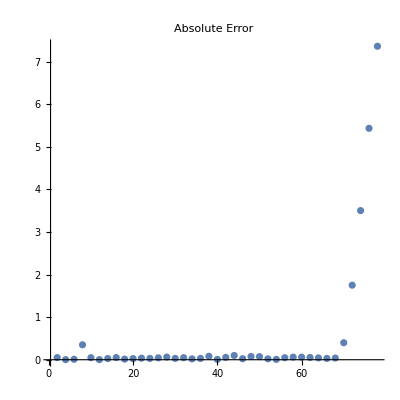

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

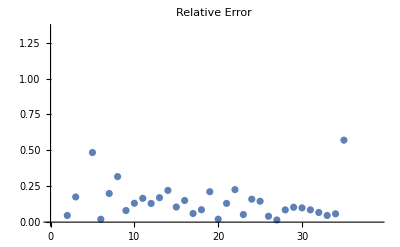

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors[[;;-6]]]
```

0.323481